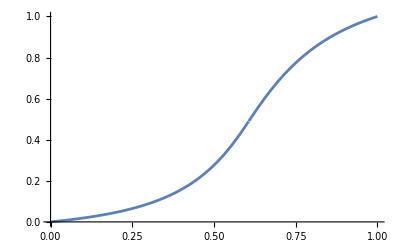

0.4894370895738783411+(2.4 (-10./(10.+normLog2Max)+x))/(1.+3.71806401235912021 ((-10./(10.+normLog2Max)+x)/If[x<10./(10.+normLog2Max),-1. equationScale[1.-1. xPivot,1.-1. yPivot,kPower,kSlope],equationScale[xPivot,yPivot,kPower,kSlope]])^(3/2))^(2/3)

(3/5)^(5/6)/2^(5/12)+(12 (-10/(10+normLog2Max)+x))/(5 (1+(-1.+10.1916140486600568 (normLog2Max/(10.+normLog2Max))^(3/2))/(normLog2Max/(-10+(10+normLog2Max) x))^(3/2))^(2/3))

(3/5)^(5/6)/2^(5/12)+(12 (-10+(10+normLog2Max) x))/(5 (10+normLog2Max) (1+(-1.+343.37727269124985696 (1/(10.+normLog2Max))^(3/2))/(10 √10 (1/(10-(10+normLog2Max) x))^(3/2)))^(2/3))

0.4894370895738783411+(2.4 (-10./(10.+normLog2Max)+x))/((1.+(-1.+10.1916140486600568 (normLog2Max/(10.+normLog2Max))^(3/2))/(normLog2Max/(-10.+(10.+normLog2Max) x))^(3/2))^(2/3))

0.4894370895738783411+(2.4 (-10.+(10.+normLog2Max) x))/((10.+normLog2Max) (1.+(0.03162277660168379332 (-1.+343.37727269124985696 (1/(10.+normLog2Max))^(3/2)))/(1/(10.-1. (10.+normLog2Max) x))^(3/2))^(2/3))

```mathematica
(*Agx Config*)
kNormLog2Min=Rationalize[-10.0];
kMidGray=Rationalize[0.18];
kPower=Rationalize[1.5];
kSlope=Rationalize[2.4];

(*AgX*)
equationScale[transitionX_,transitionY_, power_, slope_]:=Module[
{termA, termB},
termA = (slope*(Rationalize[1.0-transitionX]))^(Rationalize[-1.0*power]);
termB =  SetPrecision[((slope*(Rationalize[1.0-transitionX]))/(Rationalize[1.0 - transitionY]))^(power) - 1.0, 20];
 (termA * termB)^(Rationalize[-1.0 / power])
];

exponentialCurve[x_,scaleInput_, xPivot_, yPivot_, power_, slope_]:=(scaleInput * exponential[(slope*(x-xPivot))/scaleInput, power])+yPivot

exponential[x_, power_]:=x / ((1+(x^power))^(1/power))

logEncodingLog2[lin_, normLog2Max_]:=Module[{lg2},
lg2=Log2[lin/kMidGray];
(lg2-kNormLog2Min)/(normLog2Max-kNormLog2Min)];

calculateSigmoid[x_, normLog2Max_]:= Module[{scaleValue},
(*x=logEncodingLog2[x,normLog2Max]*)

xPivot=Abs[kNormLog2Min]/(normLog2Max-kNormLog2Min);
yPivot=kMidGray^(Rationalize[1.0/2.4]);

scaleValue = If[x<xPivot,-1*equationScale[1.0-xPivot,1.0-yPivot,kPower, kSlope],equationScale[xPivot,yPivot,kPower, kSlope]];exponentialCurve[x,scaleValue, xPivot,yPivot, kPower, kSlope]
];

(*Calculate OpenColorIO allocation for log2 from open domain \\ tristimulus value*)
calculateOCIOLog2[inEV_,odMiddleGrey_]:=Log2[2^inEV*odMiddleGrey];

(*Debug*)
Plot[calculateSigmoid[x, 6.5],{x,0,1}]

N[Simplify[calculateSigmoid[x, normLog2Max]],20]
Assuming[x>=(Abs[kNormLog2Min]/(normLog2Max-kNormLog2Min)) ,Simplify[calculateSigmoid[x,normLog2Max]]]
Assuming[x<Abs[kNormLog2Min]/(normLog2Max-kNormLog2Min),Simplify[calculateSigmoid[x, normLog2Max]]]
Assuming[x>=Abs[kNormLog2Min]/(normLog2Max-kNormLog2Min),N[Simplify[calculateSigmoid[x, normLog2Max]],20]]
Assuming[x<Abs[kNormLog2Min]/(normLog2Max-kNormLog2Min),N[Simplify[calculateSigmoid[x, normLog2Max]],20]]
(*N[calculateOCIOLog2[kNormLog2Min,Rationalize[kMidGray]],20]
N[calculateOCIOLog2[kMaxEV,Rationalize[kMidGray]],20]*)
```